```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.01,1,0]],A:=Inverse[β[ω,0.01,1,0]],B:=Inverse[β[ω,0.01,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T1.Inverse[IdentityMatrix[1]-B.T2.J.T2].B.T1].A,4000]; J=J]
```

```mathematica
LEFT1[ω_,δ_,t_,ϵ_,N_]:=Module[{J=Inverse[β[ω,0.01,1,0]],A:=Inverse[β[ω,0.01,1,0]],B:=Inverse[β[ω,0.01,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T1.Inverse[IdentityMatrix[1]-B.T2.J.T2].B.T1].A,N]; J=J]
```

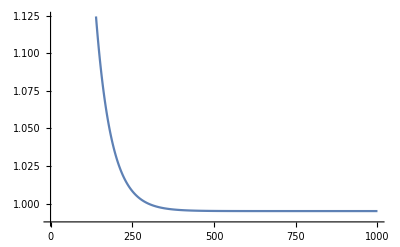

```mathematica
ListLinePlot[Table[{N,-Im[LEFT1[0,0.001,1,0,N][[1,1]]]},{N,10,1000}]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0,0.001,1,0]
```

0.999984

```mathematica
g[0,0.001,1,0]
```

{{0.-1000. ⅈ}}

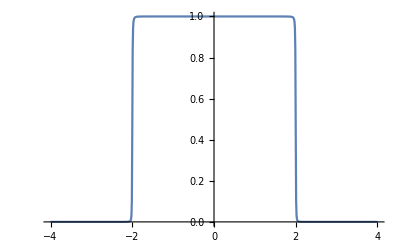

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.001,1,0]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
imp[ω_,δ_,t_,ϵ1_]:= Inverse[(ω+ⅈ*δ-ϵ1)IdentityMatrix[1]]
```

```mathematica
device1[ω_,δ_,t_,ϵ_,ϵ1_,n_]:= Module[{j=LEFT[ω,0.01,1,0],g=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1]},Do[j=Inverse[IdentityMatrix[1]-g.T.j.T].g,n-1];j=j]
```

```mathematica
device2[ω_,δ_,t_,ϵ_,ϵ1_,n_]:= Inverse[IdentityMatrix[1]-imp[ω,δ,t,ϵ1].T1[t].device1[ω,δ,t,ϵ,ϵ1,n].T1[t]].imp[ω,δ,t,ϵ1]
```

```mathematica
device3[ω_,δ_,t_,ϵ_,ϵ1_,n_]:= Module[{j=device2[ω,0.01,t,ϵ,ϵ1,n],g=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1]},Do[j=Inverse[IdentityMatrix[1]-g.T.j.T].g,50-n];j=j]
```

```mathematica
device4[ω_,δ_,t_,ϵ_,ϵ1_,n_,m_]:= Module[{j=device3[ω,0.01,t,ϵ,ϵ1,n],g=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1]},Do[j=Inverse[IdentityMatrix[1]-g.T.j.T].g,m-1];j=j]
```

```mathematica
device5[ω_,δ_,t_,ϵ_,ϵ1_,n_,m_]:= Inverse[IdentityMatrix[1]-imp[ω,δ,t,ϵ1].T1[t].device4[ω,δ,t,ϵ,ϵ1,n,m].T1[t]].imp[ω,δ,t,ϵ1]
```

```mathematica
device6[ω_,δ_,t_,ϵ_,ϵ1_,n_,m_]:= Module[{j=device5[ω,0.01,t,ϵ,ϵ1,n,m],g=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1]},Do[j=Inverse[IdentityMatrix[1]-g.T.j.T].g,50-m];j=j]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,n_,m_]:= Module[{device=device6[ω,δ,t,ϵ,ϵ1,n,m],sr=SR[ω,δ,t,ϵ]},Il1:=Inverse[IdentityMatrix[1]-device.T1[t].sr.T1[t]].device;
Ir1:=Inverse[IdentityMatrix[1]-sr.T1[t].device.T1[t]].sr;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= sr.T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1]; Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
tr2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{n=RandomInteger[{1,50}],m=RandomInteger[{1,50}]},(*Print[n];Print[m];*)tr1[ω,δ,t,ϵ,ϵ1,n,m]]
```

```mathematica
tr2[0,0.01,1,0,1]
```

0.781292

```mathematica
tr2[0,0.001,1,0,1]
```

0.586744

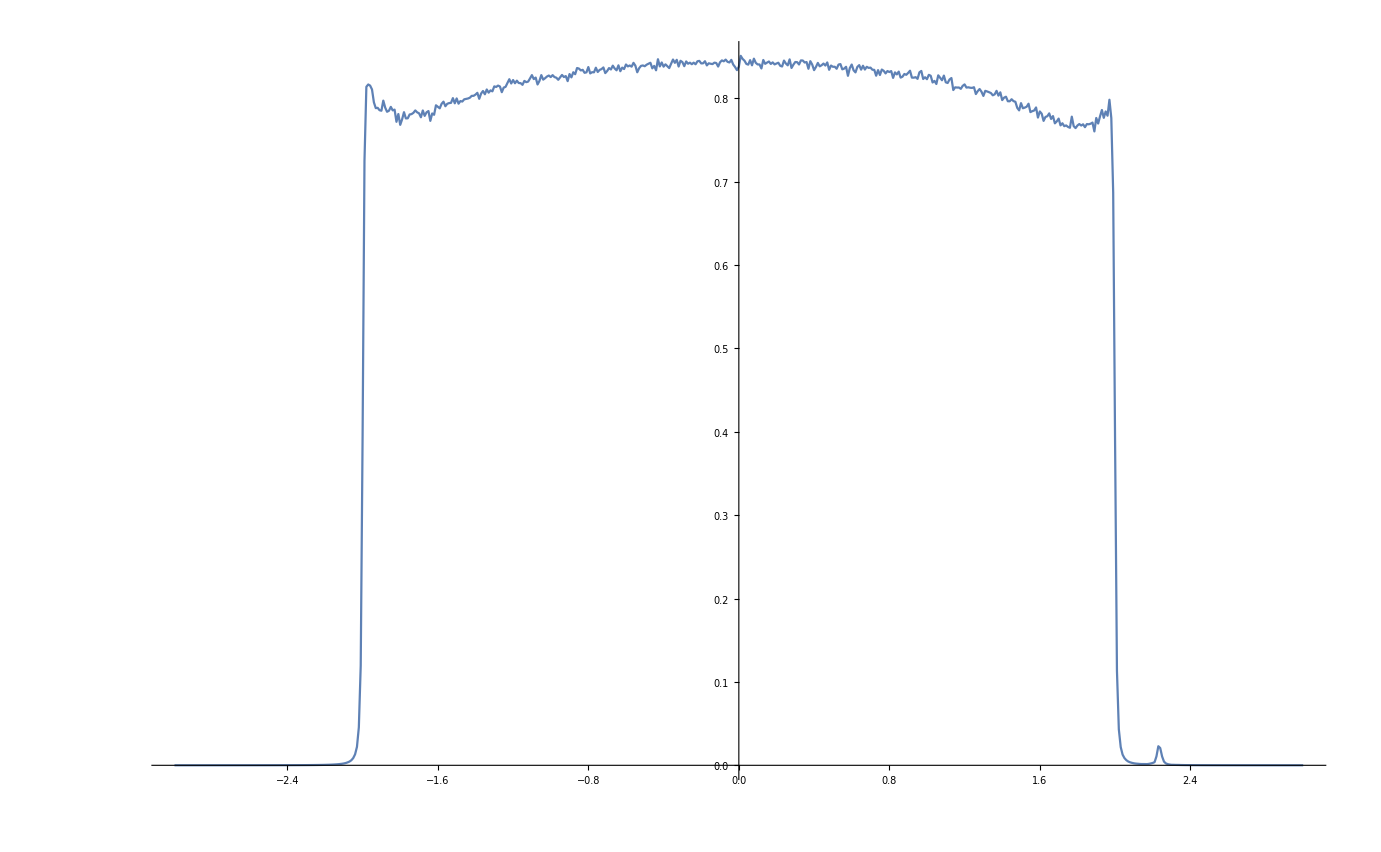

```mathematica
ListLinePlot[Table[{ω,Mean[Table[tr2[ω,0.01,1,0,1],{1000}]]},{ω,Range[-3,3,0.01]}]]
```

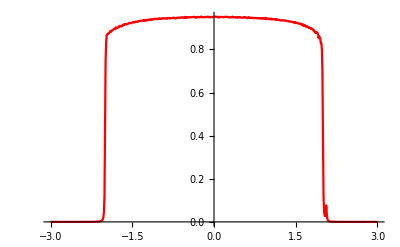

```mathematica
ListLinePlot[Table[{ω,Mean[Table[tr2[ω,0.01,1,0,0.5],{1000}]]},{ω,Range[-3,3,0.01]}],PlotStyle->Red]
```

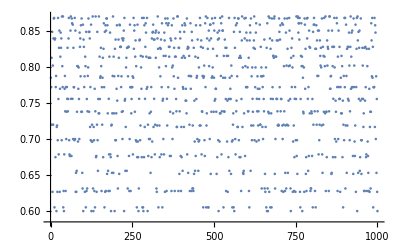

```mathematica
ListPlot[%125]
```

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.01,1,0,0.5,RandomInteger[{1,50}]],100]]},{ω,Range[-4,4,0.01]}]
```

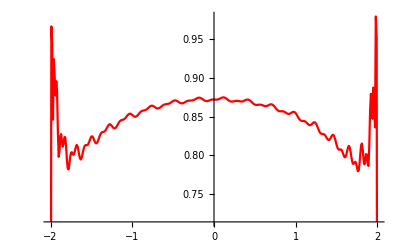

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.001,1,0,1,30]},{ω,Range[-2,2,0.01]}],PlotStyle->Red]
```

```mathematica
f[n_,m_]:=Integrate[Interpolation[Table[{ω,(tr1[ω,0.001,1,0,0.5,n]-tr1[ω,0.001,1,0,0.5,m])^2},{ω,Range[-1.8,1.8,0.01]}]][ω],{ω,-1.8,1.8}]
```

```mathematica
Show[ListLinePlot[Table[{ω,(tr1[ω,0.001,1,0,0.5,40]-tr1[ω,0.001,1,0,0.5,50])^2},{ω,Range[-1.8,1.8,0.01]}],PlotStyle->Red](*,ListLinePlot[Table[{ω,},{ω,Range[-1.8,1.8,0.01]}]]*)]
```